# Configuration Space Analysis

Basing on parallel parametrization

## General Functions

### Get Element

```mathematica
ClearAll[getElement]
getElement[array_, i_] := array[[Mod[i - 1, Length[array]] + 1]]
```

#### Testing:

```mathematica
a={1,2,3};
getElement[a,0]
Clear[a]
```

3

### Trigonometric Inverse functions

#### ArcSine

```mathematica
Clear[getAnglesASin,aSin]
getAnglesASin[x_, interval:{start_, end_}:{0, 2*Pi}] := 
  Module[
{y}, Quiet[Cases[(Reduce[#1, y] & ) /@ 
      LogicalExpand[Reduce[Reduce[Sin[y] == x, y] && 
         Inequality[start, LessEqual, y, Less, end], y]], 
     y == (yrhs_)?NumericQ :> yrhs, {2}]]
]
aSin[x_]:=Module[{tmp},
tmp=getAnglesASin[x];
If[Length[tmp]==0,tmp={Pi/2,Pi/2};];
Return[tmp];
]
```

#### ArcCos

```mathematica
Clear[getAnglesACos,aCos]
getAnglesACos[x_, interval:{start_, end_}:{0, 2*Pi}] := 
Module[{y}, Quiet[Cases[(Reduce[#1, y] & ) /@
LogicalExpand[Reduce[Reduce[Cos[y] == x, y] &&
Inequality[start, LessEqual, y, Less, end], y]],y == (yrhs_)?NumericQ :> yrhs, {2}]
]
];
aCos[x_]:=Module[{tmp},
tmp=getAnglesACos[x];
If[Length[tmp]==0,
tmp={0,0};
];
Return[tmp];
]
```

#### Tests

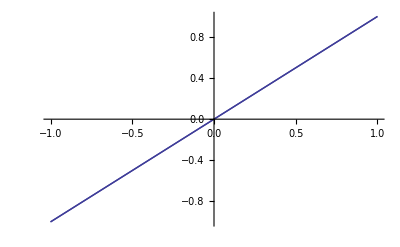

```mathematica
Plot[Cos[aCos[x]],{x,-1,1}]
```

```mathematica
Plot[Sin[aSin[x]],{x,-1,1}]
```

-Graphics-

### Equality Test

```mathematica
isEqual[x_,y_]:=If[Chop[Abs[x-y],10^(-6)]==0,
Return[True],
Return[False]
]
```

## Robot-Obstacle

### Robot

```mathematica
setRob[r_,alpha_]:=Module[{j,tmpAngle},
ClearAttributes[robR,Protected];
ClearAttributes[robA,Protected];
ClearAll[robA,robR];
robR=r;(*Robot's Radii*)
robA=alpha;(*Robot's Angles*)
SetAttributes[robA,Protected];
SetAttributes[robR,Protected];
ClearAttributes[robDelta,Protected];
ClearAll[robDelta];
robDelta=Table[0,{Length[robA]}];
For[j=1, j<Length[robR]+1,j++,
v1=a[j-1,{0,0},0]-a[j,{0,0},0];
v2=a[j+1,{0,0},0]-a[j,{0,0},0];
tmpAngle=getAnglesACos[(1/(Norm[v1] Norm[v2]))Dot[v1,v2]];
Clear[v1,v2];
If[tmpAngle[[1]]<Pi,
robDelta[[j]]=tmpAngle[[1]],
robDelta[[j]]=tmpAngle[[2]]];
];
SetAttributes[robDelta,Protected];
]
setRob::usage="setRob[r,α] defines a robot with radii vector r and angles vector α";
```

#### Fundamental Transformation

```mathematica
ClearAttributes[a,Protected];
ClearAll[a];
a[i_,r_,θ_]:=r+getElement[robR,i]{Cos[θ+getElement[robA,i]],Sin[θ+getElement[robA,i]]};
a::usage="a[i,r,θ] is the position of Subscript[a, i], in (r,θ) configuration";
SetAttributes[a,Protected];
```

#### Normals

```mathematica
ClearAttributes[robN,Protected];
ClearAll[robN];
robN[i_,r_,θ_]:=RotationMatrix[Pi/2].(a[i+1,r,θ]-a[i,r,θ])
robN::usage="a[i,r,θ] is the normal to the i-th edge in (r,θ) configuration";
SetAttributes[robN,Protected];
```

#### Boundary Vertex

```mathematica
ClearAttributes[{ait,rit,alphait},Protected];
ClearAll[ait,rit,alphait];
ait[i_,t_,r_,θ_]:=(1-t)a[i,r,θ]+t a[i+1,r,θ];
ait::usage="ait[i,t,r,θ] returns the position of ai,t in the (r,θ) configuration";
rit[i_,t_]:=Norm[ait[i,t,{0,0},0]];
rit::usage="rit[i,t] returns the radius of Subscript[a, i,t]";
alphait[i_,t_]:=Module[{tmp,Ai,res},
If[
(*Condition*)
Chop[ait[i,t,0,0][[1]]]==0,
(*Then*)
tmp=Pi/2;,
(*Else*)
tmp=ArcTan[ait[i,t,0,0][[2]]/ait[i,t,0,0][[1]]];
];
Ai=N[getElement[robA,i]];
While[tmp<Ai,
tmp=tmp+Pi;
];
res=tmp;
Return[res]
];
alphait::usage="alphait[i,t] returns the angle of Subscript[a, i,t]";
SetAttributes[{ait,rit,alphait},Protected];
```

```mathematica
Manipulate[Show[plotRob[{x,y},a],Graphics[Point[ait[0,t,{x,y},a]]]],{t,0,1},{x,-2,2},{y,-2,2},{a,0,2Pi}]
```

#### Plotting

```mathematica
ClearAll[plotRob];
plotRob[r_,θ_]:=Graphics[
{
{Green,Opacity[0.3],Polygon[Table[a[i,r,θ],{i,Length[robR]}]]},{Table[a[i,r,θ],{i,Length[robR]}]/.{x_,y_}:>{Blue,PointSize[0.02],Point[{x,y}]}},
{Table[a[i,r,θ],{i,Length[robR]}]/.{x_,y_}:>Text[Style[Position[Table[a[i,r,θ],{i,Length[robR]}],{x,y}],Darker[Green]],{x,y},{0,-1}]},
Point[{r}]
}
];
plotRob::usage="plotRob[r,θ] plots the robot in the (r,θ) configuration";
```

```mathematica
Manipulate[Show[plotRob[{x,y},t],Graphics[Point[{{-8,-8},{8,8}}]]],{x,-4,4},{y,-4,4},{t,0,2Pi}]
```

Show::gcomb: Could not combine the graphics objects in plotRob[{-4, -4}, 0], GraphicsBox[PointBox[List[List[-8, -8], List[8, 8]]]].

### Obstacle

```mathematica
setObst[vec_]:=Module[{j,tmpAngle},
ClearAttributes[b,Protected];
ClearAll[b];
b=vec;
SetAttributes[b,Protected];
ClearAttributes[obstGamma,Protected];
ClearAll[obstGamma];
obstGamma=Table[0,{Length[b]}];
For[j=1, j<Length[b]+1,j++,
v1=getElement[b,j-1]-getElement[b,j];
v2=getElement[b,j+1]-getElement[b,j];
tmpAngle=getAnglesACos[(1/(Norm[v1] Norm[v2]))Dot[v1,v2]];
Clear[v1,v2];
If[tmpAngle[[1]]<Pi,
obstGamma[[j]]=tmpAngle[[1]],
obstGamma[[j]]=tmpAngle[[2]]];
];
SetAttributes[obstGamma,Protected];
plotObst=Graphics[
{
{Red,Polygon[b]},
{b/.{x_,y_}:>{Blue,PointSize[0.02],Point[{x,y}]}},
{b/.{x_,y_}:>Text[Style[Position[b,{x,y}],Brown],{x,y},{0,-1}]}
}
];
]
setObst::usage="setObst[v] sets an obstacle with vertices vector v, computes inner angles and its plot";
```

### Plotting the Work Space

```mathematica
setRob[{1,2,1},{0,2Pi/3,6Pi/4}]
setObst[{{1,1},{2,3},{-2,4}}]
```

```mathematica
Manipulate[Show[Graphics[Point[{{0,0},{-8,-8},{8,8}}]],plotRob[{x,y},θ],plotObst],{{x,0},-10,10},{{y,0},-10,10},{{θ,0},0,2Pi}]
```

Show::gcomb: Could not combine the graphics objects in GraphicsBox[PointBox[List[List[0, 0], List[-8, -8], List[8, 8]]]], GraphicsBox[List[List[RGBColor[0, 1, 0], Opacity[0.3`], PolygonBox[List[]]], List[List[]], List[List[]], PointBox[List[List[0, 0]]]]], plotObst.

## Rotating About Boundary Vertex

### Parametrization

```mathematica
qITr[i_,t_,P_,ϕ_]:=P+rit[i,t]{Cos[ϕ+alphait[i,t]+Pi],Sin[ϕ+alphait[i,t]+Pi]};
qITr::usage="qITr[i,t,P,ϕ] is the vector component of the parametrization";
qITa[i_,t_,ϕ_]:=ϕ;
qITa::usage="qITa[i,t,ϕ] is the angular component of the parametrization";
```

#### Test

```mathematica
i=1;
P={3,1};
Manipulate[
Show[
plotRob[qITr[i,t,P,ϕ],qITa[i,t,ϕ]],
Graphics[{Red,Point[ait[i,t,qITr[i,t,P,ϕ],qITa[i,t,ϕ]]]}],
Graphics[Point[{{-5,-5},{5,5}}]],
plotRob[{0,0},0]
],
{ϕ,0,2Pi},{t,0,1}
]
```

Show::gcomb: Could not combine the graphics objects in plotRob[qITr[i, 0.386`, P, 2.701769682087222`], qITa[i, 0.386`, 2.701769682087222`]], GraphicsBox[List[RGBColor[1, 0, 0], PointBox[ait[i, 0.386`, qITr[i, 0.386`, P, 2.701769682087222`], qITa[i, 0.386`, 2.701769682087222`]]]]], GraphicsBox[PointBox[List[List[-5, -5], List[5, 5]]]], plotRob[{0, 0}, 0].

Part::pspec: Part specification 1 + Mod[-1 + i, 4] is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in plotRob[qITr[i, 0.386`, P, 2.701769682087222`], qITa[i, 0.386`, 2.701769682087222`]], GraphicsBox[List[RGBColor[1, 0, 0], PointBox[ait[i, 0.386`, qITr[i, 0.386`, P, 2.701769682087222`], qITa[i, 0.386`, 2.701769682087222`]]]]], GraphicsBox[PointBox[List[List[-5, -5], List[5, 5]]]], plotRob[{0, 0}, 0].

## Vertex-Edge Contact

### ϕ_min and ϕ_range

```mathematica
veContact[i_,j_]:=Module[
{M,v,res,x,y,phi12,phi34,phiRange,phiMin},
M={
{
getElement[robR,i+1]Cos[getElement[robA,i+1]]-getElement[robR,i]Cos[getElement[robA,i]],getElement[robR,i]Sin[getElement[robA,i]]-getElement[robR,i+1]Sin[getElement[robA,i+1]]
},
{
getElement[robR,i+1]Sin[getElement[robA,i+1]]-getElement[robR,i]Sin[getElement[robA,i]],
getElement[robR,i+1]Cos[getElement[robA,i+1]]-getElement[robR,i]Cos[getElement[robA,i]]
}
};
v=(Norm[a[i+1,{0,0},0]-a[i,{0,0},0]]/Norm[getElement[b,j+1]-getElement[b,j]])(getElement[b,j+1]-getElement[b,j]);
res=-Inverse[M].v;
x=res[[1]];
y=res[[2]];
phi12=N[aCos[x]];(* The expressions are evaluated to avoid problems related to the symbolic computation *)
phi34=N[aSin[y]];
If[isEqual[phi12[[1]],phi34[[1]]]||isEqual[phi12[[1]],phi34[[2]]],
phiMin=phi12[[1]],
If[isEqual[phi12[[2]],phi34[[1]]]||isEqual[phi12[[2]],phi34[[2]]],
phiMin=phi12[[2]],
Print["Error in evContact - problem with Subscript[ϕ, min] values"];
]
];
phiMin=Mod[phiMin,2Pi];
phiRange=Pi-getElement[robDelta,i];
If[Not[0<=phiRange<=Pi],
Print["Error in veContact - phiRange outside of bounds"];
];
Return[{phiMin,phiRange}]
]
veContact::usage="veContact[i,j]={phiMin,phiRange} of the Subscript[v, i]-Subscript[e, j] contact";
```

### Visualization functions for V-E contact

```mathematica
patchVEContact[i_,j_,col_]:=Module[{res,phiMin,phiMax,thickness},
thickness=0.005;
res=veContact[i,j];
phiMin=res[[1]];
phiMax=phiMin+res[[2]];
If[phiMax<=2Pi,
(* Patch is connected *)
Show[
ParametricPlot3D[(*Plot the patch*)
{qITr[
i,0,(1-t)getElement[b,j]+t getElement[b,j+1],phi][[1]],
qITr[
i,0,(1-t)getElement[b,j]+t getElement[b,j+1],phi][[2]],
qITa[i,0,phi]},
{t,0,1},{phi,phiMin,phiMax},Mesh->None,PlotStyle->RGBColor[col]
],
ParametricPlot3D[(*Plots V-V contact curve*)
{qITr[
i,0,getElement[b,j],phi][[1]],
qITr[
i,0,getElement[b,j],phi][[2]],
qITa[i,0,phi]},
{phi,phiMin,phiMax},PlotStyle->{Thickness[thickness],Blue}
],
ParametricPlot3D[
{qITr[
i,0,getElement[b,j+1],phi][[1]],
qITr[
i,0,getElement[b,j+1],phi][[2]],
qITa[i,0,phi]},
{phi,phiMin,phiMax},PlotStyle->{Thickness[thickness],Blue}
],
ParametricPlot3D[(*Plots E-E contact curve*)
{qITr[
i,0,(1-t)getElement[b,j]+t getElement[b,j+1],phiMin][[1]],
qITr[
i,0,(1-t)getElement[b,j]+t getElement[b,j+1],phiMin][[2]],
qITa[i,0,phiMin]},
{t,0,1},PlotStyle->{Thickness[thickness],Yellow}
],
ParametricPlot3D[
{qITr[
i,0,(1-t)getElement[b,j]+t getElement[b,j+1],phiMax][[1]],
qITr[
i,0,(1-t)getElement[b,j]+t getElement[b,j+1],phiMax][[2]],
qITa[i,0,phiMax]},
{t,0,1},PlotStyle->{Thickness[thickness],Yellow}
]
](*CASE End of connected patch*),
(* Patch is disconnected *)
Show
[(*Plot patch's parts*)
ParametricPlot3D[
{qITr[i,0,(1-t)getElement[b,j]+t getElement[b,j+1],phi][[1]],
qITr[i,0,(1-t)getElement[b,j]+t getElement[b,j+1],phi][[2]],
qITa[i,0,phi]
},{t,0,1},{phi,phiMin,2Pi},Mesh->None,PlotStyle->RGBColor[col]
],
ParametricPlot3D[
{qITr[i,0,(1-t)getElement[b,j]+t getElement[b,j+1],phi][[1]],
qITr[i,0,(1-t)getElement[b,j]+t getElement[b,j+1],phi][[2]],
qITa[i,0,phi]
},{t,0,1},{phi,0,Mod[phiMax,2Pi]},Mesh->None,PlotStyle->RGBColor[col]
],
ParametricPlot3D[(*Plots V-V contact curve*)
{qITr[
i,0,getElement[b,j],phi][[1]],
qITr[
i,0,getElement[b,j],phi][[2]],
qITa[i,0,phi]},
{phi,phiMin,2Pi},Mesh->None,PlotStyle->{Thickness[thickness],Blue}
],
ParametricPlot3D[
{qITr[
i,0,getElement[b,j+1],phi][[1]],
qITr[
i,0,getElement[b,j+1],phi][[2]],
qITa[i,0,phi]},
{phi,phiMin,2Pi},Mesh->None,PlotStyle->{Thickness[thickness],Blue}
],
ParametricPlot3D[
{qITr[
i,0,getElement[b,j],phi][[1]],
qITr[
i,0,getElement[b,j],phi][[2]],
qITa[i,0,phi]},
{phi,0,Mod[phiMax,2Pi]},Mesh->None,PlotStyle->{Thickness[thickness],Blue}
],
ParametricPlot3D[
{qITr[
i,0,getElement[b,j+1],phi][[1]],
qITr[
i,0,getElement[b,j+1],phi][[2]],
qITa[i,0,phi]},
{phi,0,Mod[phiMax,2Pi]},Mesh->None,PlotStyle->{Thickness[thickness],Blue}
],
ParametricPlot3D[(*Plots E-E contact curve*)
{qITr[
i,0,(1-t)getElement[b,j]+t getElement[b,j+1],phiMin][[1]],
qITr[
i,0,(1-t)getElement[b,j]+t getElement[b,j+1],phiMin][[2]],
qITa[i,0,phiMin]},
{t,0,1},Mesh->None,PlotStyle->{Thickness[thickness],Yellow}
],
ParametricPlot3D[(*Plots E-E contact curve*)
{qITr[
i,0,(1-t)getElement[b,j]+t getElement[b,j+1],Mod[phiMax,2Pi]][[1]],
qITr[
i,0,(1-t)getElement[b,j]+t getElement[b,j+1],Mod[phiMax,2Pi]][[2]],
qITa[i,0,Mod[phiMax,2Pi]]},
{t,0,1},Mesh->None,PlotStyle->{Thickness[thickness],Yellow}
]
](*End of disconnected patch*)
](*END of IF statement*)
]
```

```mathematica
showVEContact[i_,j_]:=Module[{res,phiMin,phiMax},
res=veContact[i,j];
phiMin=res[[1]];
phiMax=phiMin+res[[2]];
Manipulate[
{Show
[
Graphics[Point[{{-6,-6},{6,6}}]],
plotRob[
qITr[i,0,(1-t)getElement[b,j]+t getElement[b,j+1],phi],qITa[i,0,phi]
],
plotObst
],
Show[
patchVEContact[i,j,{1,1,0.}],
Graphics3D[Point[
{
qITr[i,0,(1-t)getElement[b,j]+t getElement[b,j+1],phi][[1]],
qITr[i,0,(1-t)getElement[b,j]+t getElement[b,j+1],phi][[2]],
Mod[qITa[i,0,phi],2Pi]
}
]
]
]
},
{t,0,1},{phi,phiMin,phiMax}
]
]
```

### Tests

```mathematica
showVEContact[1,1]
```

```mathematica
Table[showVEContact[i,j],{i,1,3},{j,1,3}]
```

{{,,},{,,},{,,}}

Show::gcomb: Could not combine the graphics objects in GraphicsBox[PointBox[List[List[-6, -6], List[6, 6]]]], plotRob[qITr[1, 0, getElement[b, 1], 4.456893606736168`], qITa[1, 0, 4.456893606736168`]], plotObst.

Show::gcomb: Could not combine the graphics objects in patchVEContact[1, 1, {1, 1, 0.`}], Graphics3DBox[Point3DBox[List[1, 0, Mod[qITa[1, 0, 4.456893606736168`], Times[2, Pi]]]]].

Show::gcomb: Could not combine the graphics objects in GraphicsBox[PointBox[List[List[-6, -6], List[6, 6]]]], plotRob[qITr[1, 0, getElement[b, 2], 5.242291770133616`], qITa[1, 0, 5.242291770133616`]], plotObst.

Show::gcomb: Could not combine the graphics objects in patchVEContact[1, 2, {1, 1, 0.`}], Graphics3DBox[Point3DBox[List[1, 0, Mod[qITa[1, 0, 5.242291770133616`], Times[2, Pi]]]]].

Show::gcomb: Could not combine the graphics objects in GraphicsBox[PointBox[List[List[-6, -6], List[6, 6]]]], plotRob[qITr[1, 0, getElement[b, 3], 1.637051507543017`], qITa[1, 0, 1.637051507543017`]], plotObst.

Show::gcomb: Could not combine the graphics objects in patchVEContact[1, 3, {1, 1, 0.`}], Graphics3DBox[Point3DBox[List[1, 0, Mod[qITa[1, 0, 1.637051507543017`], Times[2, Pi]]]]].

Show::gcomb: Could not combine the graphics objects in GraphicsBox[PointBox[List[List[-6, -6], List[6, 6]]]], plotRob[qITr[2, 0, getElement[b, 1], 2.100699116543823`], qITa[2, 0, 2.100699116543823`]], plotObst.

Show::gcomb: Could not combine the graphics objects in patchVEContact[2, 1, {1, 1, 0.`}], Graphics3DBox[Point3DBox[List[2, 0, Mod[qITa[2, 0, 2.100699116543823`], Times[2, Pi]]]]].

Show::gcomb: Could not combine the graphics objects in GraphicsBox[PointBox[List[List[-6, -6], List[6, 6]]]], plotRob[qITr[2, 0, getElement[b, 2], 2.8860972799412714`], qITa[2, 0, 2.8860972799412714`]], plotObst.

Show::gcomb: Could not combine the graphics objects in patchVEContact[2, 2, {1, 1, 0.`}], Graphics3DBox[Point3DBox[List[2, 0, Mod[qITa[2, 0, 2.8860972799412714`], Times[2, Pi]]]]].

Show::gcomb: Could not combine the graphics objects in GraphicsBox[PointBox[List[List[-6, -6], List[6, 6]]]], plotRob[qITr[2, 0, getElement[b, 3], 5.564042324530258`], qITa[2, 0, 5.564042324530258`]], plotObst.

Show::gcomb: Could not combine the graphics objects in patchVEContact[2, 3, {1, 1, 0.`}], Graphics3DBox[Point3DBox[List[2, 0, Mod[qITa[2, 0, 5.564042324530258`], Times[2, Pi]]]]].

Show::gcomb: Could not combine the graphics objects in GraphicsBox[PointBox[List[List[-6, -6], List[6, 6]]]], plotRob[qITr[3, 0, getElement[b, 1], 5.742765806909002`], qITa[3, 0, 5.742765806909002`]], plotObst.

Show::gcomb: Could not combine the graphics objects in patchVEContact[3, 1, {1, 1, 0.`}], Graphics3DBox[Point3DBox[List[3, 0, Mod[qITa[3, 0, 5.742765806909002`], Times[2, Pi]]]]].

Show::gcomb: Could not combine the graphics objects in GraphicsBox[PointBox[List[List[-6, -6], List[6, 6]]]], plotRob[qITr[3, 0, getElement[b, 2], 0.24497866312686378`], qITa[3, 0, 0.24497866312686378`]], plotObst.

Show::gcomb: Could not combine the graphics objects in patchVEContact[3, 2, {1, 1, 0.`}], Graphics3DBox[Point3DBox[List[3, 0, Mod[qITa[3, 0, 0.24497866312686378`], Times[2, Pi]]]]].

Show::gcomb: Could not combine the graphics objects in GraphicsBox[PointBox[List[List[-6, -6], List[6, 6]]]], plotRob[qITr[3, 0, getElement[b, 3], 2.922923707715851`], qITa[3, 0, 2.922923707715851`]], plotObst.

Show::gcomb: Could not combine the graphics objects in patchVEContact[3, 3, {1, 1, 0.`}], Graphics3DBox[Point3DBox[List[3, 0, Mod[qITa[3, 0, 2.922923707715851`], Times[2, Pi]]]]].

```mathematica
Show[
Table[
patchVEContact[i,j,{RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]}],{i,1,3},{j,1,3}
],
PlotRange->All
]
```

-Graphics3D-

## Edge-Vertex Contact

### ϕ_min and ϕ_range

```mathematica
evContact[i_,t_,j_]:=Module[{M,v,res,x,y,phi12,phi34,phiRange,phiMin},
M={
{
getElement[robR,i+1]Cos[getElement[robA,i+1]]-rit[i,t]Cos[alphait[i,t]],rit[i,t]Sin[alphait[i,t]]-getElement[robR,i+1]Sin[getElement[robA,i+1]]
},
{
getElement[robR,i+1]Sin[getElement[robA,i+1]]-rit[i,t]Sin[alphait[i,t]],
getElement[robR,i+1]Cos[getElement[robA,i+1]]-rit[i,t]Cos[alphait[i,t]]
}
};
v=(Norm[a[i+1,{0,0},0]-a[i,{0,0},0]]/Norm[getElement[b,j]-getElement[b,j-1]])(getElement[b,j]-getElement[b,j-1]);
res=-(1-t)Inverse[M].v;
x=res[[1]];
y=res[[2]];
phi12=N[aCos[x]];(* The expressions are evaluated to avoid problems related to the symbolic computation *)
phi34=N[aSin[y]];
If[isEqual[phi12[[1]],phi34[[1]]]||isEqual[phi12[[1]],phi34[[2]]],
phiMin=phi12[[1]],
If[isEqual[phi12[[2]],phi34[[1]]]||isEqual[phi12[[2]],phi34[[2]]],
phiMin=phi12[[2]],
Print["Error in evContact - problem with Subscript[ϕ, min] values"];
]
];
phiMin=Mod[phiMin,2Pi];
phiRange=Pi-getElement[obstGamma,j];
Return[{phiMin,phiRange}]
]
evContact::usage="evContact[i,j]={phiMin,phiRange} of the e_i-v_j contact";
```

### Visualization functions for E-V contact

```mathematica
patchEVContact[i_,j_,col_]:=Module[{res,phiMin,phiMax,thickness},
thickness=0.005;
res=evContact[i,0.5,j];
phiMin=res[[1]];
phiMax=phiMin+res[[2]];
If[phiMax<=2Pi,
(* Patch is connected *)
Show[
ParametricPlot3D[
{
qITr[i,t,getElement[b,j],phi][[1]],
qITr[i,t,getElement[b,j],phi][[2]],
qITa[i,t,phi]
},{t,0,1},{phi,phiMin,phiMax},Mesh->None,PlotStyle->RGBColor[col]
],(*Plot V-V contact curve*)
ParametricPlot3D[
{
qITr[i,0,getElement[b,j],phi][[1]],
qITr[i,0,getElement[b,j],phi][[2]],
qITa[i,0,phi]
},{phi,phiMin,phiMax},PlotStyle->{Blue,Thickness[thickness]}
],
ParametricPlot3D[
{
qITr[i,1,getElement[b,j],phi][[1]],
qITr[i,1,getElement[b,j],phi][[2]],
qITa[i,1,phi]
},{phi,phiMin,phiMax},PlotStyle->{Blue,Thickness[thickness]}
],(*Plot E-E contact curve*)
ParametricPlot3D[
{
qITr[i,t,getElement[b,j],phiMin][[1]],
qITr[i,t,getElement[b,j],phiMin][[2]],
qITa[i,t,phiMin]
},{t,0,1},PlotStyle->{Yellow,Thickness[thickness]}
],
ParametricPlot3D[
{
qITr[i,t,getElement[b,j],phiMax][[1]],
qITr[i,t,getElement[b,j],phiMax][[2]],
qITa[i,t,phiMax]
},{t,0,1},PlotStyle->{Yellow,Thickness[thickness]}
]
],
(* Patch is disconnected *)
Show
[
ParametricPlot3D[
{qITr[i,t,getElement[b,j],phi][[1]],
qITr[i,t,getElement[b,j],phi][[2]],
qITa[i,t,phi]
},{t,0,1},{phi,phiMin,2Pi},Mesh->None,PlotStyle->RGBColor[col]
],
ParametricPlot3D[
{qITr[i,t,getElement[b,j],phi][[1]],
qITr[i,t,getElement[b,j],phi][[2]],
qITa[i,t,phi]
},{t,0,1},{phi,0,Mod[phiMax,2Pi]},Mesh->None,PlotStyle->RGBColor[col]
],
(*Plot V-V contact curve*)
ParametricPlot3D[
{
qITr[i,0,getElement[b,j],phi][[1]],
qITr[i,0,getElement[b,j],phi][[2]],
qITa[i,0,phi]
},{phi,phiMin,2Pi},PlotStyle->{Blue,Thickness[thickness]}
],
ParametricPlot3D[
{
qITr[i,1,getElement[b,j],phi][[1]],
qITr[i,1,getElement[b,j],phi][[2]],
qITa[i,1,phi]
},{phi,phiMin,2Pi},PlotStyle->{Blue,Thickness[thickness]}
],
ParametricPlot3D[
{
qITr[i,0,getElement[b,j],phi][[1]],
qITr[i,0,getElement[b,j],phi][[2]],
qITa[i,0,phi]
},{phi,0,Mod[phiMax,2Pi]},PlotStyle->{Blue,Thickness[thickness]}
],
ParametricPlot3D[
{
qITr[i,1,getElement[b,j],phi][[1]],
qITr[i,1,getElement[b,j],phi][[2]],
qITa[i,1,phi]
},{phi,0,Mod[phiMax,2Pi]},PlotStyle->{Blue,Thickness[thickness]}
],
(*Plot E-E contact curve*)
ParametricPlot3D[
{
qITr[i,t,getElement[b,j],phiMin][[1]],
qITr[i,t,getElement[b,j],phiMin][[2]],
qITa[i,t,phiMin]
},{t,0,1},PlotStyle->{Yellow,Thickness[thickness]}
],
ParametricPlot3D[
{
qITr[i,t,getElement[b,j],Mod[phiMax,2Pi]][[1]],
qITr[i,t,getElement[b,j],Mod[phiMax,2Pi]][[2]],
qITa[i,t,Mod[phiMax,2Pi]]
},{t,0,1},PlotStyle->{Yellow,Thickness[thickness]}
]
]
](*End of IF statmenet*)
]
```

```mathematica
patchEVContact[1,1,{1,1,0}]
```

-Graphics3D-

```mathematica
showEVContact[i_,j_]:=Module[{P,res,phiMin,phiMax},
P=getElement[b,j];
res=evContact[i,0.5,j];
phiMin=res[[1]];
phiMax=phiMin+res[[2]];
Manipulate[
Show[
plotObst,
plotRob[qITr[i,t,P,ϕ],qITa[i,t,ϕ]]
],
{ϕ,phiMin,phiMax},{t,0,1}
]
]
```

```mathematica
showEVContact[4,4]
```

## Playground

### Set a Test Case

```mathematica
setRob[{0.5,1,2},{0,3Pi/4,3Pi/2}]
setObst[{{3,5},{2,4},{2,3}}]
```

### Vertex Egde contact

```mathematica
{phiMin,phiR}=veContact[1,1];
Manipulate[
{
Show[
Graphics[Point[{{-2,3},{5,7}}]],
plotRob[
{qITr[
1,0,(1-t)getElement[b,1]+t getElement[b,1+1],phi][[1]],qITr[
1,0,(1-t)getElement[b,1]+t getElement[b,1+1],phi][[2]]
},qITa[1,0,phi]
],
plotObst,
ImageSize->Medium
],
Show[
patchVEContact[1,1,{1,0,1}],
Graphics3D[{Black,Sphere[
{qITr[
1,0,(1-t)getElement[b,1]+t getElement[b,1+1],phi][[1]],qITr[
1,0,(1-t)getElement[b,1]+t getElement[b,1+1],phi][[2]]
,qITa[1,0,phi]
},0.05]}
],PlotRange->All,ImageSize->Medium
]
},
{phi,phiMin,phiMin+phiR},{t,0,1}
]
```

### Edge-Vertex Example

```mathematica
t=0.25;
{phiMin,phiR}=evContact[1,t,1];
Manipulate[
{
Show[
Graphics[Point[{{2,2},{6,6}}]],
plotRob[
{qITr[
1,t,getElement[b,1],phi][[1]],
qITr[
1,t,getElement[b,1],phi][[2]]
},qITa[1,t,phi]
],
plotObst,ImageSize->Medium
],
Show[
patchEVContact[1,1,{1,0,1}],
Graphics3D[
{
Black,Sphere
[
{qITr[
1,t,getElement[b,1],phi][[1]],
qITr[
1,t,getElement[b,1],phi][[2]],
qITa[1,t,phi]
},
0.05
]
}
],
PlotRange->All,ImageSize->Medium
]
},
{phi,phiMin,phiMin+phiR}
]
```